```mathematica
Lx=100
Ly=100;
A=Lx*Ly;
```

100

```mathematica
m0 = 0.5;
```

```mathematica
LineChernListP1 = Import["dataPTB/dataPTBlocalChernSitesOnLineLx=100Ly=100m0=1.75Xup=22Xdn=12PartsPerThousand=106Irrational.dat"];
```

```mathematica
LineChernListP2 = Import["dataPTB/dataPTBlocalChernSitesOnLineLx=100Ly=100m0=-1.75Xup=22Xdn=12PartsPerThousand=106Irrational.dat"];
```

```mathematica
list1 = Table[LineChernListP1[[ii]][[3]],{ii,1,Lx}]
```

{-13.2677,-6.87102,-3.38923,-1.53636,-0.407139,0.16708,0.533185,0.716171,0.820683,0.893375,0.92724,0.95002,0.961656,0.968079,0.9726,0.975196,0.976026,0.977301,0.977695,0.977588,0.978127,0.977684,0.977846,0.977875,0.977164,0.977872,0.977843,0.97767,0.978126,0.977672,0.977849,0.977884,0.977187,0.977912,0.977907,0.977798,0.978317,0.977905,0.978292,0.978293,0.977906,0.978319,0.977801,0.977913,0.977923,0.977206,0.977923,0.977913,0.977801,0.978319,0.977906,0.978293,0.978292,0.977905,0.978317,0.977798,0.977907,0.977912,0.977187,0.977885,0.97785,0.977674,0.978129,0.977674,0.97785,0.977885,0.977187,0.977912,0.977907,0.977797,0.978316,0.977903,0.978289,0.978287,0.977894,0.978299,0.977769,0.977849,0.977818,0.977034,0.977582,0.977354,0.976702,0.976524,0.975019,0.972694,0.969404,0.960836,0.951084,0.933387,0.893812,0.8389,0.742549,0.544781,0.241738,-0.365903,-1.33993,-3.14542,-6.46989,-12.7275}

```mathematica
list2 = Table[LineChernListP2[[ii]][[3]],{ii,1,Lx}]
```

{13.2677,6.87102,3.38923,1.53636,0.407139,-0.16708,-0.533185,-0.716171,-0.820683,-0.893375,-0.92724,-0.95002,-0.961656,-0.968079,-0.9726,-0.975196,-0.976026,-0.977301,-0.977695,-0.977588,-0.978127,-0.977684,-0.977846,-0.977875,-0.977164,-0.977872,-0.977843,-0.97767,-0.978126,-0.977672,-0.977849,-0.977884,-0.977187,-0.977912,-0.977907,-0.977798,-0.978317,-0.977905,-0.978292,-0.978293,-0.977906,-0.978319,-0.977801,-0.977913,-0.977923,-0.977206,-0.977923,-0.977913,-0.977801,-0.978319,-0.977906,-0.978293,-0.978292,-0.977905,-0.978317,-0.977798,-0.977907,-0.977912,-0.977187,-0.977885,-0.97785,-0.977674,-0.978129,-0.977674,-0.97785,-0.977885,-0.977187,-0.977912,-0.977907,-0.977797,-0.978316,-0.977903,-0.978289,-0.978287,-0.977894,-0.978299,-0.977769,-0.977849,-0.977818,-0.977034,-0.977582,-0.977354,-0.976702,-0.976524,-0.975019,-0.972694,-0.969404,-0.960836,-0.951084,-0.933387,-0.893812,-0.8389,-0.742549,-0.544781,-0.241738,0.365903,1.33993,3.14542,6.46989,12.7275}

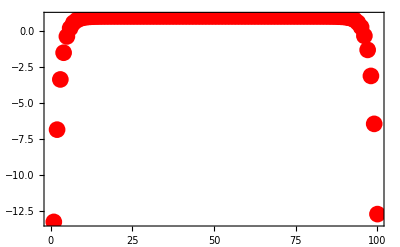

```mathematica
ListPlot[list1,PlotRange->All,Frame->True,PlotStyle-> {Red,PointSize[0.03]},Axes->False]
```

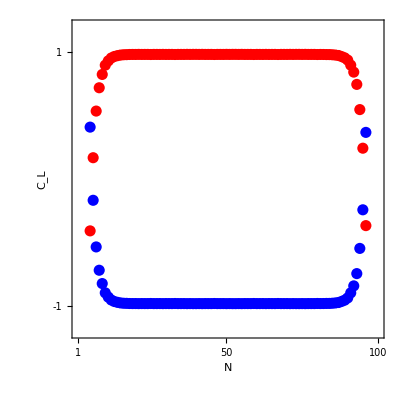

```mathematica
Show[(**Plot[1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
Plot[-1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],**)
ListPlot[list1,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list2,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-1,"-1"},{1,"1"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1,
FrameLabel->{"N","C_L"},RotateLabel->False]
```